```mathematica
(* FIG.1 RIGHT PANEL *)
```

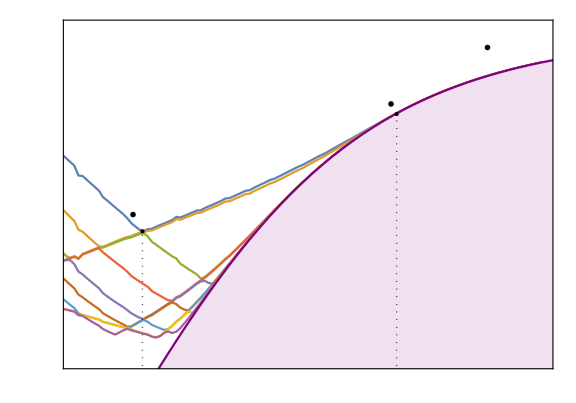

```mathematica
dataeigen = Import["PATH TO eigenvalues-alpha_3.dat"];

Neigen = 9; (* maximum of 9 *)
avec = dataeigen[[All,1]];
lambda1vec = dataeigen[[All,2]];
lambda2vec=dataeigen[[All,3]];
lambda3vec=dataeigen[[All,4]];

dataplot1 = Transpose@{avec,lambda1vec};
dataplot2=Transpose@{avec,lambda2vec};
dataplot3=Transpose@{avec,lambda3vec};

Rfun[α_,a_]:=1-(α+1)*2^((α-1)/2)*(Gamma[(α+1)/2]-Gamma[(α+1)/2,a^2/2])/a^(α+1);

LineOpt=Line[{{1.37,0},{1.37,0.695}}];
LineLoc=Line[{{2.72,0},{2.72,0.87}}];
Show[ListLinePlot[Table[Transpose@{dataeigen[[All,1]],dataeigen[[All,i+1]]},{i,1,Neigen}]],Plot[Rfun[3,a],{a,1,3.7},PlotStyle->{Purple},Filling->Axis,FillingStyle->LightPurple],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"a","\\Lambda"},Magnification->2],FrameTicks->{{Table[{0.1*i+0.5,MaTeX[NumberForm[0.1*i+0.5,{2,1}],Magnification->2]},{i,0,5}],None},{Table[{1 + i*0.5,MaTeX[NumberForm[1+0.5*i,{2,1}],Magnification->2]},{i,0,7}],None}},ImageSize->Large,AspectRatio->0.7,PlotRange->{{1,3.5},{0.5,1}},Axes->None,Epilog->{{Directive[Black,Dotted,Thick],{LineOpt,LineLoc}},{PointSize[Large],Directive[Black],Point[{1.37,0.695}]},{PointSize[Large],Directive[Black],Point[{2.72,0.87}]},Inset[MaTeX["\\alpha=3",Magnification->2],{3.2,0.97},Scaled[{0.125,0.05}]],Inset[MaTeX["a_{\\text{opt}}",Magnification->2],{1.32,0.72},Scaled[{0.125,0.05}]],Inset[MaTeX["a^*",Magnification->2],{2.69,0.885},Scaled[{0.125,0.05}]]}]
```

```mathematica
(* FIG.1 LEFT PANEL *)
```

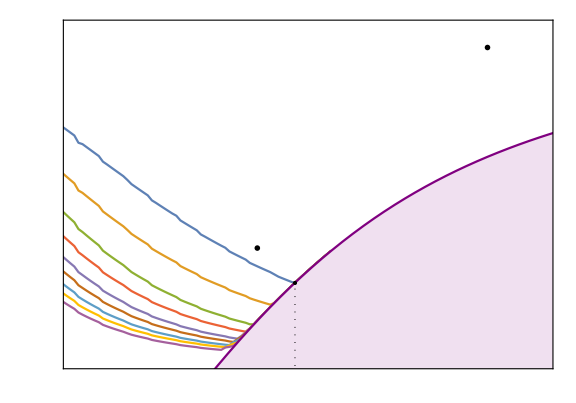

```mathematica
dataeigen = Import["PATH TO eigenvalues-alpha_1.dat"];

Neigen = 9; (* maximum of 9 *)
avec = dataeigen[[All,1]];
lambda1vec = dataeigen[[All,2]];
lambda2vec=dataeigen[[All,3]];
lambda3vec=dataeigen[[All,4]];

dataplot1 = Transpose@{avec,lambda1vec};
dataplot2=Transpose@{avec,lambda2vec};
dataplot3=Transpose@{avec,lambda3vec};

Rfun[α_,a_]:=1-(α+1)*2^((α-1)/2)*(Gamma[(α+1)/2]-Gamma[(α+1)/2,a^2/2])/a^(α+1);

LineOpt=Line[{{2.18,0},{2.18,0.617}}];
Show[ListLinePlot[Table[Transpose@{dataeigen[[All,1]],dataeigen[[All,i+1]]},{i,1,Neigen}]],Plot[Rfun[1,a],{a,1,3.7},PlotStyle->{Purple},Filling->Axis,FillingStyle->LightPurple],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"a","\\Lambda"},Magnification->2],FrameTicks->{{Table[{0.1*i+0.5,MaTeX[NumberForm[0.1*i+0.5,{2,1}],Magnification->2]},{i,0,5}],None},{Table[{1 + i*0.5,MaTeX[NumberForm[1+0.5*i,{2,1}],Magnification->2]},{i,0,7}],None}},ImageSize->Large,AspectRatio->0.7,PlotRange->{{1,3.5},{0.5,1}},Axes->None,Epilog->{{Directive[Black,Dotted,Thick],{LineOpt}},{PointSize[Large],Directive[Black],Point[{2.18,0.618}]},Inset[MaTeX["\\alpha=1",Magnification->2],{3.2,0.97},Scaled[{0.125,0.05}]],Inset[MaTeX["a_{\\text{opt}}=a^*",Magnification->2],{1.98,0.67},Scaled[{0.125,0.05}]]}]
```